# NOTES ON: Critical escape velocity for a charged particle moving around a weakly magnetized Schwarzschild black hole

## Arxiv: [1301.4633v1] DOI: 10.1103/PhysRevD.87.084043

## In this notes, we

reproduce basin plots found in Figure 5.

???

## Orbital parameters, equations of motion, and others

We begin by defining the parameters of the orbit of the charged particle before the kick, given by the azimuthal angular momentum and magnetic field strength for a charged particle orbiting at an ISCO at radius ρ0. We control the sign of l using the constant $IsPositive. For now, we make it’s default value True

```mathematica
$IsPositive=True;
l[ρ0_]:=If[$IsPositive,If[ρ0==3,√3,(ρ0 √(3ρ0-1))/(√2 √(4 ρ0^2-9ρ0 + 3 + √((3ρ0-1)(3-ρ0))))],If[ρ0==3,-√3,-(ρ0 √(3ρ0-1))/(√2 √(4 ρ0^2-9ρ0 + 3 - √((3ρ0-1)(3-ρ0))))]]
b[ρ0_]:=If[$IsPositive,If[ρ0==3,0,(√2 √(3-ρ0))/(2ρ0 √(4 ρ0^2-9ρ0 + 3 + √((3ρ0-1)(3-ρ0))))],If[ρ0==3,0,(√2 √(3-ρ0))/(2ρ0 √(4 ρ0^2-9ρ0 + 3 - √((3ρ0-1)(3-ρ0))))]]
```

The equations of motion are

```mathematica
ddrho[ρ0_] := ρ''[σ]==1/2(2ρ[σ]-3)(θ'[σ])^2+(2l[ρ0]b[ρ0]-1)/(2 ρ[σ]^2)+(l[ρ0]^2(2ρ[σ]-3))/(2 ρ[σ]^4 Sin[θ[σ]]^2)-b[ρ0]^2/2(2ρ[σ]-1)Sin[θ[σ]]^2
ddθ[ρ0_]:= θ''[σ]==-2/ρ[σ]ρ'[σ]θ'[σ]+(l[ρ0]^2 Cos[θ[σ]])/(ρ[σ]^4 Sin[θ[σ]]^3)-b[ρ0]^2 Sin[θ[σ]]Cos[θ[σ]]
```

We also define a function that checks whether or not the initial conditions are energetically forbidden. This corresponds to whether the given pair (ε,ρ) would yield an negative value for θ'[σ]^2

```mathematica
CheckEnergeticallyForbidden[ε_,ρ0_]:=Block[{ωsquared,Ueff},
Ueff = (1-1/ρ0)(1 + ((l[ρ0]-b[ρ0] ρ0^2)^2)/ρ0^2);
ωsquared = (ε^2-Ueff)/(ρ0(ρ0-1));
If[ωsquared<0,True,-√ωsquared]
];
```

## Basin Calculation Preliminaries

We have the following tests: (z > 1000) → 1, (z < -1000) → 2, (ρ ≤ 1) → 3 and (σ >MaximumT) → 4

```mathematica
Attractors = {WhenEvent[ρ[σ]Cos[θ[σ]]>1000,Throw[1]],WhenEvent[ρ[σ]Cos[θ[σ]]<-1000,Throw[2]],WhenEvent[ρ[σ]≤ 1,Throw[3]],WhenEvent[σ>MaximumT,Throw[4]]};
```

We also have the additional condition that whenever the initial kick is energetically forbidden, we assign a value of 0. We explicitly assign ρ0 = (5 + √13)/4 as energetically forbidden when l < 0. The our CheckBasin function is of the form

```mathematica
CheckAttractor[ε_,ρ0_]:=CheckAttractor[ε,ρ0]= Block[{ω0},
Catch[If[ρ0==1,Throw[3]];
If[ρ0==(5 + √13)/4&&!$IsPositive,Throw[0]];
ω0 = CheckEnergeticallyForbidden[ε,ρ0];
If[ω0,Throw[0]];
NDSolve[{ddθ[ρ0],ddrho[ρ0],ρ[0]==ρ0,ρ'[0]==0,θ[0]==π/2,θ'[0]==ω0}~Join~Attractors,{ρ,θ},{σ,0,MaximumT+1}];]
]
```

We assign the corresponding colors

```mathematica
AttractorColors={0->White,1->GrayLevel[0.5],2-> GrayLevel[0.75],3-> GrayLevel[0.25],4->Black}
```

{0→GrayLevel[1],1→GrayLevel[0.5],2→GrayLevel[0.75],3→GrayLevel[0.25],4→GrayLevel[0]}

We also launch a bunch of kernels. We shall be using the “FinestGrain” Method for evaluating ParallelTable, because of the time needed to calculate the color of each pixel varies widely. As such, we launch more kernels than is necessary for the default method.

```mathematica
LaunchKernels[6]
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local],KernelObject[5,local],KernelObject[6,local]}

```mathematica
$KernelCount
```

6

We also use the Monitor function to see the progress of our calculation. For this to work inside a parallel process, we must define a shared variable.

```mathematica
SetSharedVariable[Progress];Progress=0;
```

In the calculations that proceed, this varies between 0 and 1, and gives a general feel how near completion the current task is.

## Case 1: Positive l

We now define our maximum simulation time and the number of pixels and fix our IsPositive variable

```mathematica
MaximumT = 10^5;pixels=800;$IsPositive=True;
```

## Region 1 - {{2,0},{1,3}}

We now calculate the basins of attraction. We define our Region 1 box to be {{2,0},{1,3}}.

```mathematica
Region1ε = Subdivide[2,0,pixels];Region1ρ0 = Subdivide[1,3,pixels];Progress = 0;
BasinRegion1 = Monitor[ParallelTable[Progress=Max[N@((Region1ε⟦1⟧ - ε)/(Region1ε⟦1⟧-Region1ε⟦-1⟧)),Progress];CheckAttractor[ε,ρ0],{ε,Region1ε},{ρ0,Region1ρ0},Method->"FinestGrained"],Progress];//AbsoluteTiming
MatrixPlot[BasinRegion1,ColorRules->AttractorColors,FrameTicks->{{{1,Region1ε⟦1⟧},{pixels/2,"ε"},{pixels+1,Region1ε⟦-1⟧}},{{1,Region1ρ0⟦1⟧},{pixels/2,"ρ0"},{pixels+1,Region1ρ0⟦-1⟧}}},ImageSize->500,BaseStyle->{FontSize->24},LabelStyle->{FontSize->24}]
```

{5685.4,Null}

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]]
```

E:\Joshua\Documents\Wolfram Mathematica\Research\ChargedParticleinMagFieldSchd

```mathematica
Export["Region1N"<>ToString[pixels]<>".mx",BasinRegion1]
```

Region1N800.mx

## Region 2 - {{1.15,0.95},{2.8,3.0}}

We now calculate the basins of attraction. We define our Region 1 box to be {{1.15, 0.95}, {2.8, 3.0}}.

```mathematica
Region2ε = Subdivide[115/100,95/100,pixels];Region2ρ0 = Subdivide[28/10,3,pixels];Progress = 0;
BasinRegion2 = Monitor[ParallelTable[Progress=Max[N@((Region2ε⟦1⟧ - ε)/(Region2ε⟦1⟧-Region2ε⟦-1⟧)),Progress];CheckAttractor[ε,ρ0],{ε,Region2ε},{ρ0,Region2ρ0},Method->"FinestGrained"],Progress];//AbsoluteTiming
```

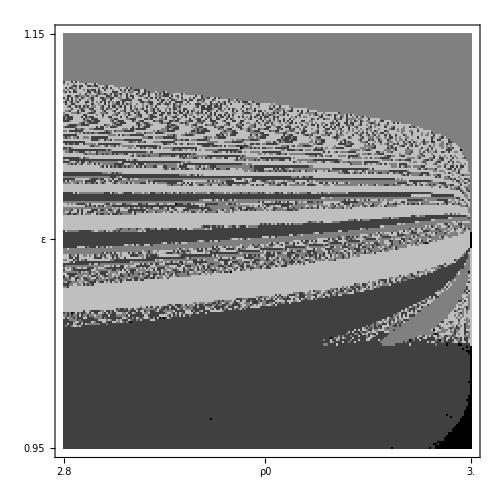

```mathematica
MatrixPlot[BasinRegion2,ColorRules->AttractorColors,FrameTicks->{{{1,N@Region2ε⟦1⟧},{pixels/2,"ε"},{pixels+1,N@Region2ε⟦-1⟧}},{{1,N@Region2ρ0⟦1⟧},{pixels/2,"ρ0"},{pixels+1,N@Region2ρ0⟦-1⟧}}},ImageSize->500,BaseStyle->{FontSize->24},LabelStyle->{FontSize->24}]
```

## Region 3 - {{1.050,0.975},{2.925,3.0}}

{501.466,Null}

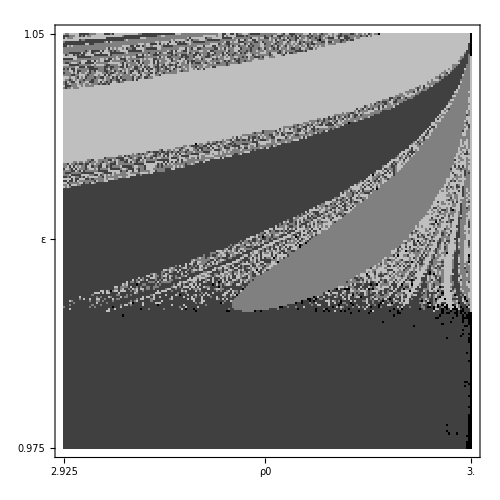

```mathematica
Region3ε = Subdivide[1050/1000,975/1000,pixels];Region3ρ0 = Subdivide[2925/1000,3,pixels];Progress = 0;
BasinRegion3 = Monitor[ParallelTable[Progress=Max[N@((Region3ε⟦1⟧ - ε)/(Region3ε⟦1⟧-Region3ε⟦-1⟧)),Progress];CheckAttractor[ε,ρ0],{ε,Region3ε},{ρ0,Region3ρ0},Method->"FinestGrained"],Progress];//AbsoluteTiming
MatrixPlot[BasinRegion3,ColorRules->AttractorColors,FrameTicks->{{{1,N@Region3ε⟦1⟧},{pixels/2,"ε"},{pixels+1,N@Region3ε⟦-1⟧}},{{1,N@Region3ρ0⟦1⟧},{pixels/2,"ρ0"},{pixels+1,N@Region3ρ0⟦-1⟧}}},ImageSize->500,BaseStyle->{FontSize->24},LabelStyle->{FontSize->24}]
```

## Region 4 - {{1.10,1.05},{2.95,3.0}}

{578.655,Null}

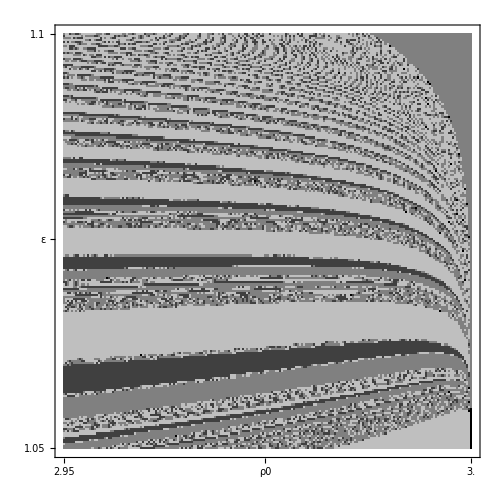

```mathematica
Region4ε = Subdivide[1100/1000,1050/1000,pixels];Region4ρ0 = Subdivide[2950/1000,3,pixels];Progress = 0;
BasinRegion4 = Monitor[ParallelTable[Progress=Max[N@((Region4ε⟦1⟧ - ε)/(Region4ε⟦1⟧-Region4ε⟦-1⟧)),Progress];CheckAttractor[ε,ρ0],{ε,Region4ε},{ρ0,Region4ρ0},Method->"FinestGrained"],Progress];//AbsoluteTiming
MatrixPlot[BasinRegion4,ColorRules->AttractorColors,FrameTicks->{{{1,N@Region4ε⟦1⟧},{pixels/2,"ε"},{pixels+1,N@Region4ε⟦-1⟧}},{{1,N@Region4ρ0⟦1⟧},{pixels/2,"ρ0"},{pixels+1,N@Region4ρ0⟦-1⟧}}},ImageSize->500,BaseStyle->{FontSize->24},LabelStyle->{FontSize->24}]
```

## Region 5 - {{1.125,1.100},{2.850,2.875}}

{1385.56,Null}

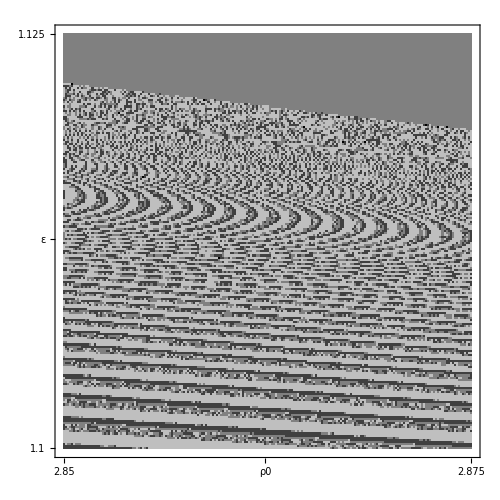

```mathematica
Region5ε = Subdivide[1125/1000,1100/1000,pixels];Region5ρ0 = Subdivide[2850/1000,2875/1000,pixels];Progress = 0;
BasinRegion5 = Monitor[ParallelTable[Progress=Max[N@((Region5ε⟦1⟧ - ε)/(Region5ε⟦1⟧-Region5ε⟦-1⟧)),Progress];CheckAttractor[ε,ρ0],{ε,Region5ε},{ρ0,Region5ρ0},Method->"FinestGrained"],Progress];//AbsoluteTiming
MatrixPlot[BasinRegion5,ColorRules->AttractorColors,FrameTicks->{{{1,N@Region5ε⟦1⟧},{pixels/2,"ε"},{pixels+1,N@Region5ε⟦-1⟧}},{{1,N@Region5ρ0⟦1⟧},{pixels/2,"ρ0"},{pixels+1,N@Region5ρ0⟦-1⟧}}},ImageSize->500,BaseStyle->{FontSize->24},LabelStyle->{FontSize->24}]
```

## Case 2: Negative l

We now define our maximum simulation time and the number of pixels and fix our IsPositive variable for the negative l case

```mathematica
MaximumT = 10^5;pixels=200;$IsPositive=False;
```

## Region 6 - {{3,1},{(5 + √13)/4,3}}

```mathematica
Region6ε = Subdivide[3,1,pixels];Region6ρ0 = Subdivide[(5+√13)/4,3,pixels];Progress = 0;
BasinRegion6 = Monitor[ParallelTable[Progress=Max[N@((Region6ε⟦1⟧ - ε)/(Region6ε⟦1⟧-Region6ε⟦-1⟧)),Progress];CheckAttractor[ε,ρ0],{ε,Region6ε},{ρ0,Region6ρ0},Method->"FinestGrained"],Progress];//AbsoluteTiming
MatrixPlot[BasinRegion6,ColorRules->AttractorColors,FrameTicks->{{{1,N@Region6ε⟦1⟧},{pixels/2,"ε"},{pixels+1,N@Region6ε⟦-1⟧}},{{1,N@Region6ρ0⟦1⟧},{pixels/2,"ρ0"},{pixels+1,N@Region6ρ0⟦-1⟧}}},ImageSize->500,BaseStyle->{FontSize->24},LabelStyle->{FontSize->24}]
```

## Acts 16:31

```mathematica
SetDirectory[NotebookDirectory[]]
Export["Region1N"<>ToString[pixels]<>".mx",BasinRegion1]
Export["Region2N"<>ToString[pixels]<>".mx",BasinRegion2]
Export["Region3N"<>ToString[pixels]<>".mx",BasinRegion3]
Export["Region4N"<>ToString[pixels]<>".mx",BasinRegion4]
Export["Region5N"<>ToString[pixels]<>".mx",BasinRegion5]
Export["Region6N"<>ToString[pixels]<>".mx",BasinRegion6]
```